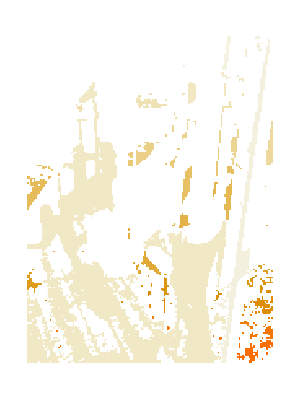
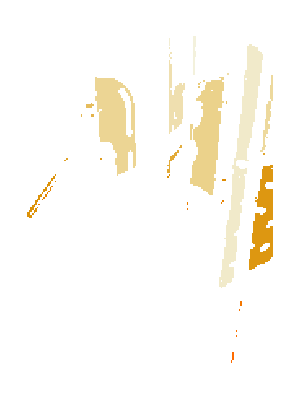
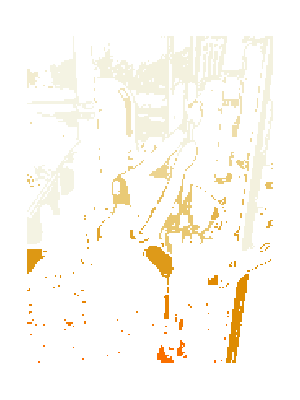
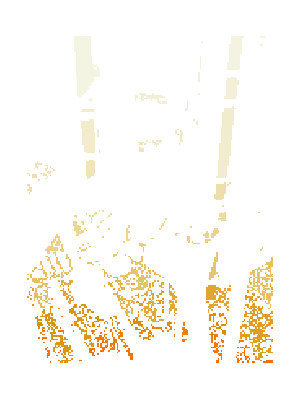
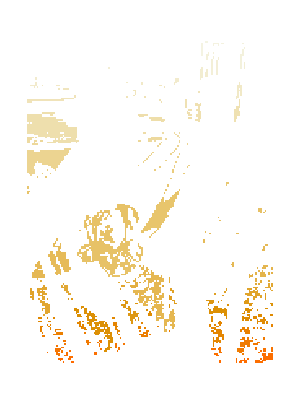
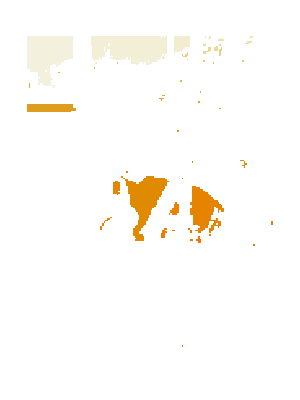
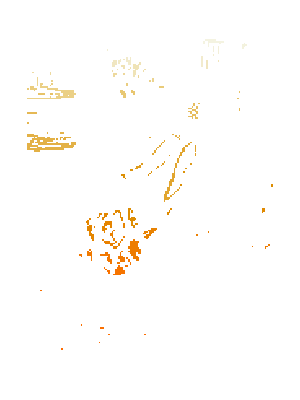
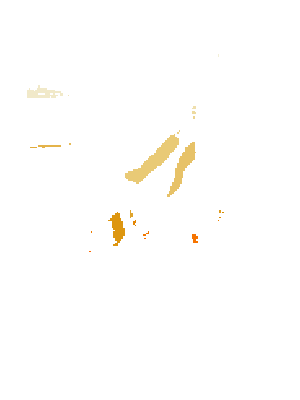
{-Graphics-,Paint Colors,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-,Paint zones,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},paint strokes will be applied in roughty this order for each paint color,{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-},-Graphics-}

```mathematica
(*Mathematica code for Army,a shoulder elbow wrist style painting robot

DO NOT RUN WITH ENABLED DYNAMICS ON RaspberryPi !  Computation time and CPU may be endlessly consumed should dynamic automatic recalculation be enabled.  
Manually calculate once with a SHIFT+ENTER on this script

*)

original=Import["/TessaPose.jpg"];  (*This is the original image, use any path to a picture on your drive you choose*)
isize=ImageDimensions[original];  (*what are the image dimensions*)
image=ImageResize[ImageAdjust[original],Floor[#/20]&/@isize,Resampling->"Linear"];
(*image is resized to a smaller size.  aiming for about 150 x 200 pixels*)
(*Resample linear because square pixels tesselate well and paint tesselates indeterminately making dithering a messy painting proposition.  
Note to my daughter Tessa:  Tesselate means cover a floor with a shape or floor tile, nothing to do with your image imported above.*)

paintingPallet={{0.823529,0.815686,0.796078},{0.05,0.05,0.05},{0.996078,0.827451,0.623529},{0.94902,0.847059,0.470588},{0.67451,0.427451,0.176471},{0.321569,0.556863,0.439216},{0.65098,0.2,0.3},{0.054902,0.407843,0.713725}};(*those are RGB values for the paint colors I have*)
With[{cols=paintingPallet},selectColor[rgb:{_,_,_}]:=First[SortBy[cols,Norm[rgb-#]&]]];img=image;reimaged=ImageApply[selectColor,img];(*Thanks to StackExchange Mathematica user Halirutan for help with "How do I ColorQuantize to a predetermined mosaic builders pallet of limited choices?" answered expertly on March 15*)
z=ImageData[reimaged];(*z is image as data points in array with three RGB pixel values*)
dim=Dimensions[z];
fz=Flatten[z,1];(*easy and fast to work with flattened image data in this instance*)
ufz=Sort[Union[fz]];(*Unitize the array into?8?component RGB colors.Paint light colors first and dark ones last for best results?*)
paintingPallet=ufz;(*the original pallet gets convered and unconvered resulting in tiny pallet color part per million changes.  Simplest to backconvert pallet to match image data values rather than swap millions of image data points or do a wobbly search and still have same ppm rounding shifts in dataset*)
colorByNumber=Flatten[Position[paintingPallet,#]&/@fz];(*color by number pixel by pixel happens on this line*)
colorByNumber=Partition[colorByNumber,dim[[2]]];(*Return colorByNumber into image array shape*)

zerorules=Rule[#,0]&/@Range[Length[paintingPallet]];(*make a matrix of rules for color separation.*)
polyrules=Table[zerorules,{Length[zerorules]}];(*aggregate those color separation rules*)
Table[polyrules[[loop,loop]]=Rule[loop,1],{loop,1,8}];(*Still building that rules matrix for image separation.*)
imageDataSeparations=Table[colorByNumber/.polyrules[[loop]],{loop,1,Length[zerorules]}];(*and we have data color separations*)
binarySeparations=Image[#]&/@imageDataSeparations;(*now I know exactly where to paint each color*)
morph=MorphologicalComponents[#,CornerNeighbors->True,Method->"Nested"]&/@binarySeparations;(*and now I know what order to paint the strokes in.Ideally each island blob of paint gets a que number for painting.And I might not have to lift the brush while I paint an isolated blob*)
countmorphsegments=Max[Flatten[#]]&/@morph;  (*starting on how to construct paint strokes from bitmap, first by counting morphological components in each paint color*)
morphbyareabystroke=(bincountmorphsegments=Counts[Flatten[#]]; Range[Max[Flatten[#]]]/.bincountmorphsegments)&/@morph; 
 (* morphbyareabystroke - organize sets of color one stroke area one, then next stroke area, till through all stroke areas and all colors*)
paintXYtable=Table[Table[Position[morph[[outloop]],loop],{loop,1,countmorphsegments[[outloop]]}],{outloop,1,Length[countmorphsegments]}];(*[[color,strokesegment]] generates list*)somanybrushstrokes=Table[(points=paintXYtable[[loop,#]];
tour=Union[FindShortestTour[points]];(*Find Shorted tour finds the shortest path thorough a stroke area pixel location.   Tours are loops though every point in the set where last point is a return to the starting location  - I use Union to elimiate duplicate points to try to eliminate stray lines in blobby paint*)
points=points[[Last[tour]]])&/@Range[countmorphsegments[[loop]]],{loop,1,Length[countmorphsegments]}];
            (*and paintXYtable should now be a table of XY values composed by paint colors and then stroke locations and paths*)

rescalebrushstrokes = Map[rescaleXY[#[[1]],#[[2]]  ]&, somanybrushstrokes, {3} ];

rescaleXY[x_,y_]:={1.75*(x-100.5)/201., 1.75*(y-75.)/201.};
XYtoE[x_,y_]:=Module[{r,out},
r=(x^2.+y^2.)^0.5;
If[r>0,out= 420./Pi*2*ArcSinh[r/2] , out= 0, out=0]   ];
XYtoS[x_,y_]:= Module[{r= (x^2.+y^2.)^.5, quad=quadrant[x,y], interiorA,e=XYtoE[x,y],asin},
If[r==0,r=0.0000001];
interiorA=(420.-e)/2; (*420 steps in half circle*)
interiorA + quad + 420/Pi*ArcSin[x/y]  ];
quadrant[x_,y_]:=  Which[
                    And[x≥ 0, y≥  0], 0.,
                    And[ x≥0, y≤ 0], 840./4,
                     And[x≤ 0 , y≤ 0], 840./2,
                     And[x ≤ 0, y≥ 0], 840.*3/4 
]  ;
XYtoSE[x_,y_]:= Module[{r= (x^2.+y^2.)^.5, quad=quadrant[x,y], e=XYtoE[x,y],s},
 If[And[ x==0,y==0], (x=0.0000001; y=0.0000001)]; 
 {quad+(420.-e)/2 +420/Pi* ArcTan[y,x],e}  ];

SE = Map[XYtoSE[#[[1]],#[[2]] ]&, rescalebrushstrokes, {3}];

SE=Round[SE];

Table[(redressXYforPython = ToString[SE[[loop]] ];pystrsings = StringReplace[redressXYforPython,{"{"-> "(","}"-> ")"}];pystrings = StringReplace[pystrings,{"((("-> "[((",")))"-> "))]"}];
 pystrings = StringJoin[pystrings] ;
Export["SEdata"<>ToString[loop]<>".py",pystrings,"Text"];),{loop,1,Length[paintingPallet]}];


{image,"Paint Colors",RGBColor[#]&/@paintingPallet,reimaged,"Paint zones",binarySeparations,"paint strokes will be applied in roughty this order for each paint color",MatrixPlot[#,Frame->False]&/@morph,Graphics[Table[{RGBColor[paintingPallet[[loop]]],Line[somanybrushstrokes[[loop]]]},{loop,1,Length[somanybrushstrokes]}]]}
```